(-ⅇ^(ⅈ π w) | -ⅇ^(-ⅈ π w) | ⅇ^(2 ⅈ √10 π w) | ⅇ^(-2 ⅈ √10 π w)
-ⅈ ⅇ^(ⅈ π w) w | ⅈ ⅇ^(-ⅈ π w) w | ⅈ √10 ⅇ^(2 ⅈ √10 π w) w | -ⅈ √10 ⅇ^(-2 ⅈ √10 π w) w
-ⅇ^(2 ⅈ kx π) | -ⅇ^(2 ⅈ kx π) | ⅇ^(4 ⅈ √10 π w) | ⅇ^(-4 ⅈ √10 π w)
ⅇ^(2 ⅈ kx π) w | -ⅇ^(2 ⅈ kx π) w | -√10 ⅇ^(4 ⅈ √10 π w) w | √10 ⅇ^(-4 ⅈ √10 π w) w)

-ⅈ ⅇ^(-ⅈ π w-2 ⅈ √10 π w) (-11 ⅇ^(2 ⅈ kx π)-2 √10 ⅇ^(2 ⅈ kx π)+11 ⅇ^(2 ⅈ kx π+2 ⅈ π w)-2 √10 ⅇ^(2 ⅈ kx π+2 ⅈ π w)+4 √10 ⅇ^(ⅈ π w+2 ⅈ √10 π w)+4 √10 ⅇ^(4 ⅈ kx π+ⅈ π w+2 ⅈ √10 π w)+11 ⅇ^(2 ⅈ kx π+4 ⅈ √10 π w)-2 √10 ⅇ^(2 ⅈ kx π+4 ⅈ √10 π w)-11 ⅇ^(2 ⅈ kx π+2 ⅈ π w+4 ⅈ √10 π w)-2 √10 ⅇ^(2 ⅈ kx π+2 ⅈ π w+4 ⅈ √10 π w))

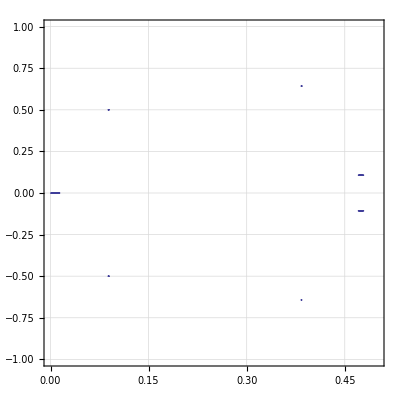

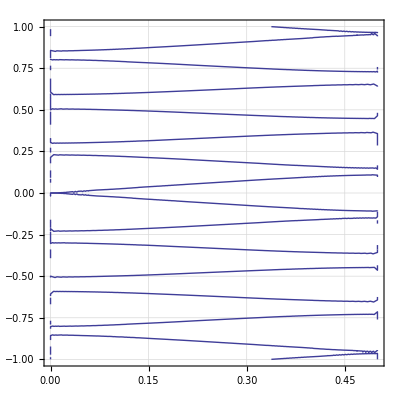

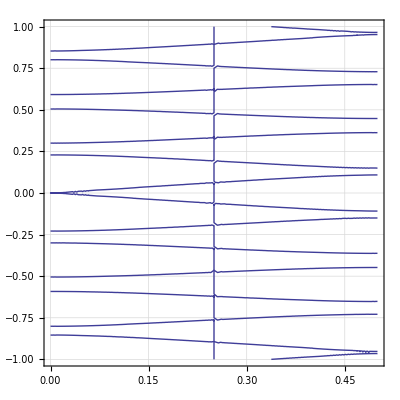

```mathematica
ClearAll["Global`*"]
epi1:=1
mu1:=1
epi2:=20
mu2:=2
a:=2*Pi(*unit cell*)
xh:=Pi(*interface point*) 
k1:=w*Sqrt[epi1*mu1]
k2:=w*Sqrt[epi2*mu2]
i:=I
Ey1l:=Exp[i*k1*xh](* e^(i k1 xh)*)
Ey1r:=Exp[-i*k1*xh](* e^(-i k1 xh)*)
Ey2l:=Exp[i*k2*xh](*e^(i k2 xh)*)
Ey2r:=Exp[-i*k2*xh](*e^(-i k2 xh)*)

Blo:=Exp[i*kx*a](*Bloch condition e^ (i k_x a)*)

A1:={-Ey1l,-Ey1r,Ey2l,Ey2r}
A2:={-i*k1/mu1*Ey1l,i*k1/mu1*Ey1r,i*k2/mu2*Ey2l,-i*k2/mu2*Ey2r}
A3:={-Blo,-Blo,Exp[i*k2*a],Exp[-i*k2*a]}
A4:={k1/mu1*Blo,-k1/mu1*Blo,-k2/mu2*Exp[i*k2*a],k2/mu2*Exp[-i*k2*a]}(*修正版 with [E'y/mu]=0 at x=a*)
(*A4:={k1*Blo,-k1*Blo,-k2*Exp[i*k2*a],k2*Exp[-i*k2*a]}*)
A:={A1,A2,A3,A4}
A//MatrixForm
det:=Factor[Det[A]]/w^2
aaa:=det
aaa
(*detfix:=det/(    (w)*( -(mu2-epi2)/(mu1*mu2)*Exp[-i*k1*xh-i*k2*xh])     )*) 
wa:=-1
wb:=1
kxa:=0
kxb:=.5
cri:=.1
ContourPlot[Abs[aaa]==cri,{kx,kxa,kxb},{w,wa,wb},GridLines->Automatic]
ContourPlot[Re[aaa]==0,{kx,kxa,kxb},{w,wa,wb},GridLines->Automatic]
ContourPlot[Im[aaa]==0,{kx,kxa,kxb},{w,wa,wb},GridLines->Automatic]
Plot3D[aaa,{w,wa,wb},{kx,kxa,kxb}];
(*exp degree too high*)
(*ContourPlot[b==0,{w,wa,wb},{kx,kxa,kxb}]
```